### From https://www.thphys.uni-heidelberg.de/~plehn/includes/notes/hunting_higgs/hunting_higgs.pdf (Eq.48) (note that in Eq.48 there is one sign wrong) τ=4 mQ^2/m_H^2

```mathematica
f[τ_]:=If[τ>1,(ArcSin[1/(√τ)]^2),-1/4(Log[(1+√(1-τ))/(1-√(1-τ))]-I Pi)^2];
F[τ_]:=3/2 τ(1+(1-τ)f[τ]);
ggH[τ_] :=-I Subscript[α, s]/(8 Pi)1/v τ(1-(1-τ)f[τ]); 
sert[x_]=Simplify[Normal[Series[Simplify[F[τ],Assumptions->τ>1]/.{τ->1/x},{x,0,3}]]];
fLight[x_]:=sert[x];
fHeavy[x_]=Simplify[
Normal[Series[Simplify[F[τ],Assumptions->τ<1],{τ,0,3}]]/.{τ->1/x}];
```

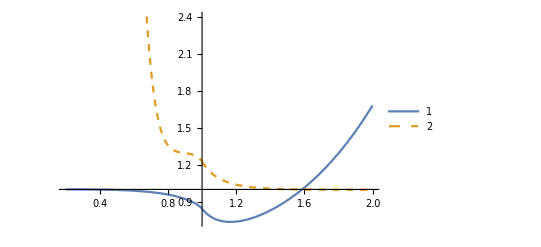

```mathematica
Plot[{Abs[sert[x]]^2/Abs[F[1/x]]^2,Abs[fHeavy[x]]^2/Abs[F[1/x]]^2},{x,0.2,2},PlotLegends->Automatic,PlotStyle->{Thick,Dashed},AxesOrigin->{1.,1.}]
```